```mathematica
f1 =Function[{u,v},(5u+v)==8][x,y];
f2 = Function[{u,v},(3u-v)==8][x,y];

getRed[ec1_, ec2_, num_, arg_] := 
If[num==1,
Reduce[ec1, arg, Reals],
Reduce[ec2, arg, Reals]
]

getValues[ec1_, ec2_, valueOneX_, valueTwoX_, valueOneY_, valueTwoY_, valueOneR_, valueTwoR_] := (
valueOneX = ec1[[1]];
equis = valueOneX[[1]];
valueOneX = equis[[1]]; (*Sirve*)
valueTwoX = ec2[[1]];
equis = valueTwoX[[1]];
valueTwoX = equis[[1]];
valueOneY = ec1[[1]];
ye = valueOneY[[2]];
valueOneY = ye[[1]];
valueTwoY = ec2[[1]];
ye = valueTwoY[[2]];
valueTwoY = ye[[1]];
valueOneR = ec1[[-1]]; (*Last*)
valueTwoR = ec2[[-1]]
)


getRed[f1,f2,1,y]
```

y==8-5 x

```mathematica
getNewIncognita[ec1_,ec2_,incog_,arg_] :=(
If[arg==y,
newIncog = ReplaceAll[ec1, x -> incog[[2]]],
newIncog = ReplaceAll[ec2, y -> incog[[2]]]
];
Return[reducedNewIncog = Reduce[newIncog]]
)

mainSust[ec1_,ec2_,num_,arg_]:=(
Print["Método de sustitución"];
res = getRed[ec1,ec2,num,arg]; (*Creo que aquí obtengo el resultado ya reducido*)
(*  y==8-5x *)
reduced = res[[2]];
replaced = ReplaceAll[ec2,y-> reduced];
incog = Reduce[replaced]; (*Aquí saco una incognita*)
(*Solve[replaced]*)
Print[incog];
newIncog = getNewIncognita[ec1,ec2,incog, arg];
Print[newIncog]
)
mainSust[f1, f2,1,y]
```

Método de sustitución

x==2

y==-2

```mathematica
pruebas[fun_, n_]:=(
fun[[n]]
)
pruebas[f1, 2]
```

8

```mathematica
mainIgualacion[ec1_,ec2_,num_,arg_] := (
reducedFirst = Reduce[ec1, arg, Reals];
reducedSecond = Reduce[ec2, arg, Reals];
replaced = ReplaceAll[reducedFirst, arg -> reducedSecond[[2]]];
incog = Reduce[replaced];(*Aquí obtengo la primera incognita*)
Print[incog];
newIncog = getNewIncognita[ec1,ec2,incog, arg];
Print[newIncog]

)
mainIgualacion[x+y==3, x-y == -1, 1, y](*X para obtener el valor de Y*)
```

x==1

y==2

```mathematica
mainCrammer[ec1_, ec2_, num_, arg_] :=
(
Print["Método de crammer"];
valueOneX = ec1[[1]];
equis = valueOneX[[1]];
valueOneX = equis[[1]]; (*Sirve*)
valueTwoX = ec2[[1]];
equis = valueTwoX[[1]];
valueTwoX = equis[[1]];
valueOneY = ec1[[1]];
ye = valueOneY[[2]];
valueOneY = ye[[1]];
valueTwoY = ec2[[1]];
ye = valueTwoY[[2]];
valueTwoY = ye[[1]];
valueOneR = ec1[[-1]]; (*Last*)
valueTwoR = ec2[[-1]];
(*Sacamos el determinante del sistema*)

detSistema = (valueOneX * valueTwoY) - (valueTwoX * valueOneY);(*OK*)
detX = (valueOneR * valueTwoY)-(valueTwoR * valueOneY);
detY = (valueOneX * valueTwoR)-(valueTwoX * valueOneR);
Print["Valor de X:"];
Print[(detX/detSistema)];
Print["Valor de Y:"];
Print[(detY/detSistema)]

)
mainCrammer[(5x-2y==-2),(-3x+7y==-22),1,x]
```

Método de crammer

Part::partd: Part specification (-3)⟦1⟧ is longer than depth of object.

Valor de X:

-2

Valor de Y:

-4

y==-4

x==-2

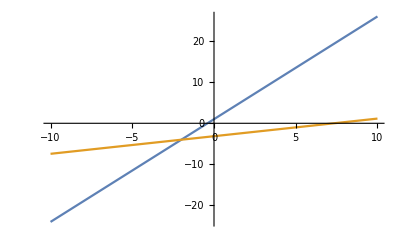

```mathematica
mainReducc[ec1_, ec2_, num_]:=(
valueOneX = ec1[[1]];
equis = valueOneX[[1]];
valueOneX = equis[[1]]; (*Sirve*)
valueTwoX = ec2[[1]];
equis = valueTwoX[[1]];
valueTwoX = equis[[1]];
valueOneY = ec1[[1]];
ye = valueOneY[[2]];
valueOneY = ye[[1]];
valueTwoY = ec2[[1]];
ye = valueTwoY[[2]];
valueTwoY = ye[[1]];
valueOneR = ec1[[-1]]; (*Last*)
valueTwoR = ec2[[-1]];

newValueXOne = valueOneX * valueTwoX;
newValueYOne = valueOneY * valueTwoX;
newValueROne = valueOneR * valueTwoX;

newValueXTwo = valueTwoX * valueOneX;
newValueYTwo = valueTwoY * valueOneX;
newValueRTwo = valueTwoR * valueOneX;

f1 =Function[{u,v},((newValueXOne - newValueXTwo)u+(newValueYOne - newValueYTwo)v)==(newValueROne - newValueRTwo)][x,y];
reduced = Reduce[f1];
equis = ReplaceAll[ec1, y -> reduced[[2]]];
Print[reduced];
Print[Reduce[equis]];
Plot[{Reduce[ec1, y][[2]], Reduce[ec2, y][[2]]}, {x, -10,10}] (*Esta es la gráfica*)
)
mainReducc[(5x-2y==-2),(-3x+7y==-22),1]
```